Ryan Foundoulis
605107291
ryanfoundoulis@gmail.com
HW4

```mathematica
(* Question 1 *)
Remove["Global`*"]
                                               

$Assumptions={Element[{k1,ω,L},Reals]  && k1>0 &&  k2 > 0  && L > 0};                                        

(* x < 0 *)
ψ1[x_,t_] = E^(I (k1 x - ω t)) + R1 E^(-I (k1 x + ω t));

(* 0 < x < L *)
ψ2[x_,t_] = T1 E^(I (k2 x - ω t)) + R2 E^(-I (k2 x + ω t));

(* L < x *)                                      
ψ3[x_, t_] = T2 E^(I (k1 x - ω t));

dψ1dx[x_,t_] = D[ψ1[x,t],x];
dψ2dx[x_,t_] = D[ψ2[x,t],x];
dψ3dx[x_,t_] = D[ψ3[x,t],x];

(* Boundary conditions *)
displacement={ψ1[0,t]==ψ2[0,t],ψ2[L,t]==ψ3[L,t]};
slope={dψ1dx[0,t]==dψ2dx[0,t],dψ2dx[L,t]==dψ3dx[L,t]};

(*************************************************************************)
(* Now... look for the transmission and reflection coefficients *)

eqnlist=Join[displacement,slope];
slist={R1,T1,R2,T2};

soln=Solve[eqnlist,slist][[1]]//Quiet;
R1=R1/.soln // FullSimplify;
T1=T1/.soln // FullSimplify;
R2=R2/.soln // FullSimplify;
T2=T2/.soln // FullSimplify;

IntR1[L_] = Re[R1^2] //FullSimplify;
IntT1[L_] = T1^2 //FullSimplify;
IntR2[L_] = R2^2 //FullSimplify;
IntT2[L_] = T2^2 //FullSimplify;

Print["At x = 0 \n"];
Print["The reflected intensities is ", IntR1[L]];Print["The transmitted intensities is ", IntT1[L]];

Print["When L = 0 \n"];
Print["The reflected intensities is ", IntR1[0]];Print["The transmitted intensities is ", IntT1[0]];
Print["Since reflection is 0, our transmission is greatest at L = 0"]

Print["\n \n At x = L \n"];
Print["The reflected intensities is ", IntR2[L]];Print["The transmitted intensities is ", IntT2[L]];

Print["When L = 0 \n"];
Print["The reflected intensities is ", IntR1[0]];Print["The transmitted intensities is ", IntT1[0]];
Print["Since reflection is 0, our transmission is greatest at L = 0"]

(* Dummy Values *)

(*Re[IntR1[L]] // FullSimplify*)

k1 = 1;
k2 = 2;

plot1 = Plot[Re[IntR1[x]], {x,0,6}];
Show[plot1, PlotLabel->"Reflection Intensity at x = 0", AxesLabel->{"L lenght","Intensity"}]

plot2 = Plot[Re[IntT1[x]], {x,0,6}];
Show[plot2, PlotLabel->"Transmission Intensity at x = 0", AxesLabel->{"L lenght","Intensity"}]
```

2 Re[(ⅇ^(0.-5 ⅈ x) Sin[0.5 x])/x]

2 Re[(ⅇ^((0.+0.5 ⅈ) t-5 ⅈ x) Sin[0.5 (-t+x)])/(-t+x)]

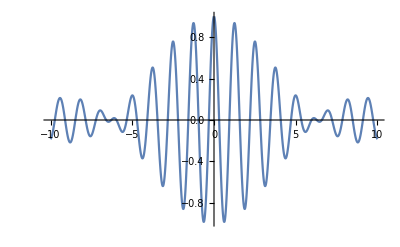

-Graphics-

```mathematica
(* Question 2 *)

Remove["Global`*"] // Quiet

$Assumptions={Element[{k0,ω,δk},Reals]  && k0>0 &&  δk > 0  && ω > 0};   

ω = ω0 + ω0p k0; 

(* A(k) is one within the bounds of the k0-δk and k0+δk *)

ψ[x_,t_] = E^(I (ω0-ω0p k0)t) Integrate[E^(I (ω0p t - x)k), {k,k0-δk,k0+δk}]  //FullSimplify ;

(*ψ[x_,t_] = Re[ψ[x,t]]//FullSimplify*)

ω0p = 1;
ω0 = .5;
k0 = 5;
δk = 0.5;

ψ1[x_] = Re[ψ[x,0]]
ψ2[x_,t_] = Re[ψ[x,t]]
Plot[ψ1[x],{x,-10,10}]

plot[t_] := Plot[ψ2[x,t],{x,-20,20},PlotRange->{{-20,20},{-1,1}}]

tlo = 0;
thi = 15;

Animate[plot[t],{t,tlo,thi}]
```

Re[ⅇ^(ⅈ (0.-5 x))]

Re[ⅇ^(ⅈ (0.5 t-5 x))]

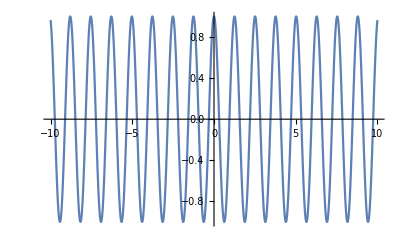

```mathematica
(* Question 3 i) *)

Remove["Global`*"] //Quiet

$Assumptions={Element[{k0,ω,δk},Reals]  && k0>0 &&  δk > 0  && ω > 0};   

ω = ω0 + ω0p k0; 

A1[k_] = DiracDelta[k-k0];

(* A(k) is one within the bounds of the k0-δk and k0+δk *)

ψ5[x_,t_] =   E^(I (ω0-ω0p k0)t)Integrate[A1[k] E^(I (ω0p t - x)k), {k,k0-δk,k0+δk}]  //FullSimplify ;

(*ψ[x_,t_] = Re[ψ[x,t]]//FullSimplify*)

ω0p = 1;
ω0 = .5;
k0 = 5;
δk = 0.5;

ψ4[x_] = Re[ψ5[x,0]]
ψ6[x_,t_] = Re[ψ5[x,t]]
Plot[ψ4[x],{x,-10,10}]

plot1[t_] := Plot[ψ6[x,t],{x,-20,20},PlotRange->{{-20,20},{-1,1}}]

tlo = 0;
thi = 15;

Animate[plot1[t],{t,tlo,thi}]
```

```mathematica
(* Question 3 ii) *)

Remove["Global`*"] //Quiet

$Assumptions={Element[{k0,ω,δk},Reals]  && k0>0 &&  δk > 0  && ω > 0};   

ω = ω0 + ω0p k0; 

A2[k_] = 1;

(* A(k) is one within the bounds of the k0-δk and k0+δk *)

ψ7[x_,t_] =   E^(I (ω0-ω0p k0)t)Integrate[A2[k] E^(I (ω0p t - x)k), {k,k0-δk,k0+δk}]  //FullSimplify ;

(*ψ[x_,t_] = Re[ψ[x,t]]//FullSimplify*)

ω0p = 1;
ω0 = .5;
k0 = 5;
δk = 0.5;

ψ8[x_] = Re[ψ7[x,0]]
ψ9[x_,t_] = Re[ψ7[x,t]]
Plot[ψ8[x],{x,-10,10}]

plot2[t_] := Plot[ψ9[x,t],{x,-20,20},PlotRange->{{-20,20},{-1,1}}]

tlo = 0;
thi = 15;

Animate[plot2[t],{t,tlo,thi}]
```

2 Re[(ⅇ^(0.-5 ⅈ x) Sin[0.5 x])/x]

2 Re[(ⅇ^((0.+0.5 ⅈ) t-5 ⅈ x) Sin[0.5 (-t+x)])/(-t+x)]

-Graphics-

6.28319 Re[(ⅇ^(ⅈ (0.-5 x)) Cos[0.5 x])/((3.14159-1. x) (π+1. x))]

6.28319 Re[(ⅇ^(ⅈ (0.5 t-5 x)) Cos[0.5 (-t+x)])/((π+1. t-1. x) (π+1. (-t+x)))]

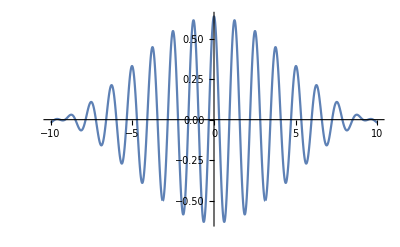

```mathematica
(* Question 3 iii) *)

Remove["Global`*"] //Quiet

$Assumptions={Element[{k0,ω,δk},Reals]  && k0>0 &&  δk > 0  && ω > 0};   

ω = ω0 + ω0p k0; 

A3[k_] = Cos[(π/(2 δk )) (k−k0)];

(* A(k) is one within the bounds of the k0-δk and k0+δk *)

ψ11[x_,t_] =   E^(I (ω0-ω0p k0)t)Integrate[A3[k] E^(I (ω0p t - x)k), {k,k0-δk,k0+δk}]  //FullSimplify ;

(*ψ[x_,t_] = Re[ψ[x,t]]//FullSimplify*)

ω0p = 1;
ω0 = .5;
k0 = 5;
δk = 0.5;

ψ10[x_] = Re[ψ11[x,0]]
ψ12[x_,t_] = Re[ψ11[x,t]]
Plot[ψ10[x],{x,-10,10}]

plot4[t_] := Plot[ψ12[x,t],{x,-20,20},PlotRange->{{-20,20},{-1,1}}]

tlo = 0;
thi = 15;

Animate[plot4[t],{t,tlo,thi}]
```

1. Re[(ⅇ^(-ⅈ (0.+5.5 x)) (-ⅇ^((0.+1. ⅈ) x)+1. (1+(0.+1. ⅈ) x)))/x^2]

1. Re[(ⅇ^(-ⅈ (0.+5.5 x)) (-ⅇ^((0.+1. ⅈ) x)+ⅇ^((0.+1. ⅈ) t) (1+(0.+1. ⅈ) (-t+x))))/(-t+x)^2]

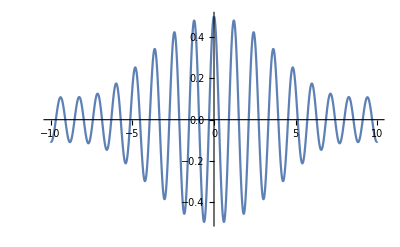

```mathematica
(* Question 3 iv) *)

Remove["Global`*"] //Quiet

$Assumptions={Element[{k0,ω,δk},Reals]  && k0>0 &&  δk > 0  && ω > 0};   

ω = ω0 + ω0p k0; 

A4[k_] =(k−k0 + δk)/(2 δk);

(* A(k) is one within the bounds of the k0-δk and k0+δk *)

ψ13[x_,t_] =   E^(I (ω0-ω0p k0)t)Integrate[A4[k] E^(I (ω0p t - x)k), {k,k0-δk,k0+δk}]  //FullSimplify ;

(*ψ[x_,t_] = Re[ψ[x,t]]//FullSimplify*)

ω0p = 1;
ω0 = .5;
k0 = 5;
δk = 0.5;

ψ14[x_] = Re[ψ13[x,0]]
ψ15[x_,t_] = Re[ψ13[x,t]]
Plot[ψ14[x],{x,-10,10}]

plot5[t_] := Plot[ψ15[x,t],{x,-20,20},PlotRange->{{-20,20},{-1,1}}]

tlo = 0;
thi = 15;

Animate[plot5[t],{t,tlo,thi}]
```

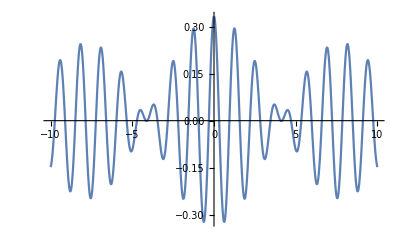

```mathematica
(* Question 3 v) *)

Remove["Global`*"] //Quiet

$Assumptions={Element[{k0,ω,δk},Reals]  && k0>0 &&  δk > 0  && ω > 0};   

ω = ω0 + ω0p k0; 

A5[k_] =(k−k0)^2/(δk)^2;

(* A(k) is one within the bounds of the k0-δk and k0+δk *)

ψ16[x_,t_] =   E^(I (ω0-ω0p k0)t)Integrate[A5[k] E^(I (ω0p t - x)k), {k,k0-δk,k0+δk}]  //FullSimplify ;

(*ψ[x_,t_] = Re[ψ[x,t]]//FullSimplify*)

ω0p = 1;
ω0 = .5;
k0 = 5;
δk = 0.5;

ψ17[x_] = Re[ψ16[x,0]];
ψ18[x_,t_] = Re[ψ16[x,t]];
Plot[ψ17[x],{x,-10,10}]

plot6[t_] := Plot[ψ18[x,t],{x,-20,20},PlotRange->{{-20,20},{-1,1}}]

tlo = 0;
thi = 15;

Animate[plot6[t],{t,tlo,thi}]
```

a)

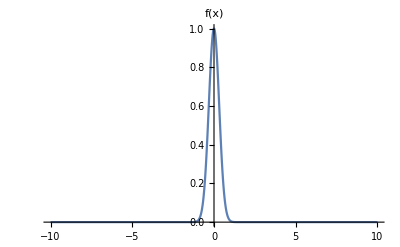

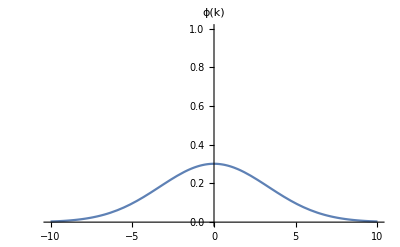

```mathematica
(* Question 4 *)

Remove["Global`*"] // Quiet

$Assumptions={Element[{n,α},Reals]  && n>0 &&  α > 0};   

n = 1;
α = 5;
σ = 1;

Print["a)"]
f[x_] = n E^(-α x^2);

Plot[f[x], {x,-10,10}, PlotLabel-> "f(x)", PlotRange->{{-10,10},{0,1}}]

ϕ[k_] = FourierTransform[f[x] E^(-1/2  (x)^2/σ^2),x,k]//FullSimplify;

Plot[ϕ[k], {k,-10,10}, PlotLabel-> "ϕ(k)", PlotRange->{{-10,10},{0,1}}]
```